```mathematica
<<Notation`
```

```mathematica
Symbolize[OverHat[x_]]
```

Per Euler-Bernoulli beam theory, assuming EI is constant, the governing equation is given by

E I (d^4 w)/(d x^4)=q(x).

And boundary conditions are given by

θ(x)=(d w)/(d x),
M(x) = -E I (d^2 w)/(d x^2),
Q(x) = -E I (d^3 w)/(d x^3).

Using (x̂=x/L,ŵ=w/L,q̂=(q L^3)/(E I), M̂=(M L)/(E I),P̂=(P L^2)/(E I)) => (θ̂(x̂)=(d ŵ)/(d x̂)=(d w)/(d x)=θ(x),(d^2 ŵ)/(d (x̂)^2)=1/L(d^2 w)/(d x^2),(d^3 ŵ)/(d (x̂)^3)=1/L^2(d^3 w)/(d x^3),(d^4 ŵ)/(d (x̂)^4)=1/L^3(d^4 w)/(d x^4)), the dimensionless equations are

(d^4 ŵ)/(d (x̂)^4)=q̂(x̂),
(d ŵ)/(d x̂)=θ̂(x̂),
- (d^2 ŵ)/(d (x̂)^2)=M̂(x̂),
- (d^3 ŵ)/(d (x̂)^3)=Q̂(x̂).

## 1. Cantilever beam

1/6 P̂ (-3+x̂) (x̂)^2

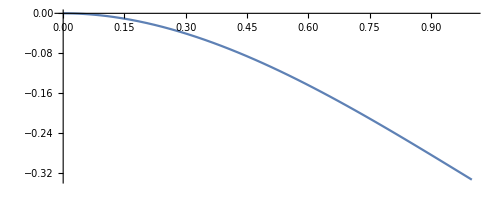

```mathematica
Solwhat1=DSolve[{ ŵ''''[x̂]==0,ŵ[0]==0,ŵ'[0]==0,ŵ''[1]==0,-ŵ'''[1]==-P̂},ŵ[x̂],{x̂,0,1}][[1]];
y1[x̂:_]=ŵ[x̂]/.Solwhat1
Plot[y1[x̂]/.P̂->1,{x̂,0,1},AspectRatio->Automatic]
```

```mathematica
y1[1]
```

-(P̂)/3

## 2. Simply-supported beam

Piecewise[{{1/48 P̂ x̂ (-3+4 (x̂)^2), 0≤x̂≤1/2}, {1/48 P̂ (-3+4 (1-x̂)^2) (1-x̂), 1/2≤x̂≤1}, {0, True}}]

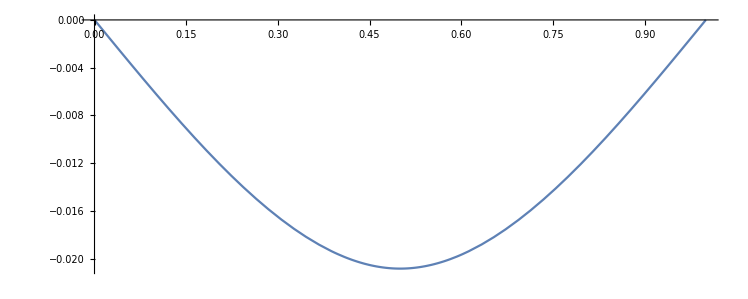

```mathematica
Solwhat2=DSolve[{ ŵ''''[x̂]==0,ŵ[0]==0,ŵ''[0]==0,ŵ'[1/2]==0,-ŵ'''[1/2]==(-P̂)/2},ŵ[x̂],{x̂,0,1/2}][[1]];
y2[x̂:_]=Piecewise[{{ŵ[x̂]/.Solwhat2,0≤x̂≤1/2},{ŵ[x̂]/.Solwhat2/.x̂->1-x̂,1/2≤x̂≤1}}]
Plot[y2[x̂]/.P̂->1,{x̂,0,1},AspectRatio->Automatic]
```

```mathematica
y2[1/2]
```

-(P̂)/48

## 3. Fixed-fixed beam

Piecewise[{{1/48 P̂ (x̂)^2 (-3+4 x̂), 0≤x̂≤1/2}, {1/48 P̂ (-3+4 (1-x̂)) (1-x̂)^2, 1/2≤x̂≤1}, {0, True}}]

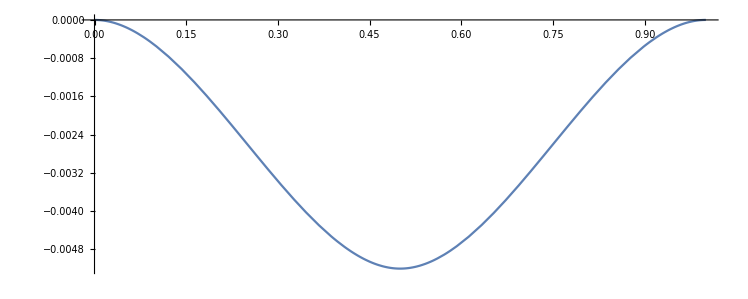

```mathematica
Solwhat3=DSolve[{ ŵ''''[x̂]==0,ŵ[0]==0,ŵ'[0]==0,ŵ'[1/2]==0,-ŵ'''[1/2]==(-P̂)/2},ŵ[x̂],{x̂,0,1/2}][[1]];
y3[x̂:_]=Piecewise[{{ŵ[x̂]/.Solwhat3,0≤x̂≤1/2},{ŵ[x̂]/.Solwhat3/.x̂->1-x̂,1/2≤x̂≤1}}]
Plot[y3[x̂]/.P̂->1,{x̂,0,1},AspectRatio->Automatic]
```

```mathematica
y3[1/2]
```

-(P̂)/192